# PIC1_AIM_vanderpol Homework Notes

## Depletion region radio frequency modulation of a dispersive Silicon waveguide

## Analysis of dynamic modulation of the junction depletion zone by impressed voltage, V(ω_rf), for a symmetric depletion region E18 Doping , 450 nm guide width, 220 nm Si thickness, symmetric spatial doping of the rib waveguide region

#### Built-in Voltage induced Junction Capacitance

```mathematica
(****Clear all variables in Kernel****)
epsilonR=.;epsilonO=.;k=.;vBuiltIn=.;
nDope=.;pDope=.;nIntrinsic=.;T=.; vBuiltIn=.; q=.;
 depletionZoneP=.;  depletionZoneN=. ;vBuiltIn=.;depletionZoneT=.;
(***** Main Functions****)
Print["Depletion N in the waveguide"]
 depletionZoneN = ((2 epsilonR epsilonO )/q )vBuiltIn (pDope/(nDope(nDope +pDope)))//Sqrt;
Print["Depletion P in the waveguide"]
 depletionZoneP= ((2 epsilonR epsilonO )/q) vBuiltIn (nDope/(pDope(nDope +pDope)))//Sqrt;
Print["Intrinsic Junction Voltage"]
 vBuiltIn=k T/q Log[nDope pDope /nIntrinsic^2];
Print["Combined Depletion P+N in the waveguide"]
 depletionZoneT = depletionZoneN +  depletionZoneP;
 intrinsicRatio =depletionZoneP/depletionZoneN ;
(* Constants: N,P in M^3 *)
epsilonR=11.9;epsilonO=8.85 10^-12;
k=1.381*10^-23;q=1.602 10^-19; T=290;
(****Relative Parameters to plot some curves****)
nIntrinsic=1.5 10^16             (*cm^-3*);                      
nDope:=1 10^18 10^6                        (* convert cm^3 to m^3 *);
pDope:=1 10^18 10^6                          (* convert cm^3 to m^3 *);
   dZT=   Plot[10^9 depletionZoneT,{nDope,1 10^23, 10^24}, Frame->True,PlotLabel->"Depletion Zone vs Ndopant"];
   dZP = Plot[10^9  depletionZoneT,{pDope,1 10^23, 10^24}, Frame->True,PlotLabel->"Depletion Zone vs Pdopant"];
Plot3D[10^9{depletionZoneT,depletionZoneN,depletionZoneP},{nDope,1 10^23,10^24},{pDope,1 10^23,10^24},PlotLabel->"Depletion Zone Wd, Xne & Xp depletion width vs doping", PlotRange->All,AxesLabel-> {"ndope","pdope", "nanometers"},PlotLegends->"Expressions"]

(****)

(*****show contants & calculate the static capacitance with no impressed junction Voltage****)
Print["+++++++++++++++++++++++++++++"]
Print["k = ",k,   "\nepsilonO= ",epsilonO,  "\nepsilonR= ",epsilonR]
Print["q = ",q,  " T= ",T,  "\nnIntrinsic= ",nIntrinsic,  "\nvBuiltIn= ",vBuiltIn]
Print["nDope = ",nDope,  "  pDope= ",pDope]
Print["  depletionZoneN  = ",  depletionZoneN ,  "   depletionZoneP= ", depletionZoneP]
Print["  depletionZoneT = ",  depletionZoneT ]
"Static built-in Junction Capacitance"//Print
StaticCapacitance =depletionZoneT^-1 220 10^-9 2.048 10^-3 epsilonO epsilonR
"Farads \n++++++++++++++++++++++++++"//Print
```

Depletion N in the waveguide

Depletion P in the waveguide

Intrinsic Junction Voltage

Combined Depletion P+N in the waveguide

-Graphics3D-

+++++++++++++++++++++++++++++

k = 1.381×10^-23
epsilonO= 8.85×10^-12
epsilonR= 11.9

q = 1.602×10^-19 T= 290
nIntrinsic= 1.5×10^16
vBuiltIn= 0.900738

nDope = 1000000000000000000000000  pDope= 1000000000000000000000000

depletionZoneN  = 2.4334×10^-8   depletionZoneP= 2.4334×10^-8

depletionZoneT = 4.8668×10^-8

Static built-in Junction Capacitance

9.74989×10^-13

Farads 
++++++++++++++++++++++++++

#### Junction Capacitance Modification by impressed Voltage Variation of Depletion Region

Depletion Zone VbuiltIn 290C Wd=48.668 nanometers
V=.5 Volts Wd=32.4619 nanometers
V=-4Volts  Wd=113.521 nanometers

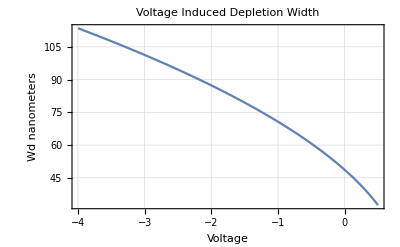

Change in Effective Index w.r.t. carrier doping Maximum=deltaindexMax

++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++
Homework 
Calculate the capcitance & effective index change vs impressed Voltage

-0.000341621

-0.000341621-indBuiltIn

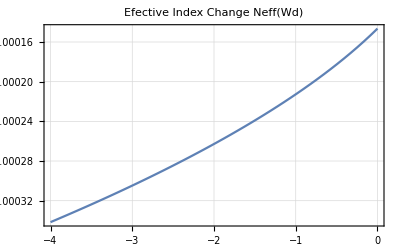

Depletion region .5,0 and -4 Volts

Wd(Vimpressed): 
.5 Volt=3.24619×10^-8
 0 Volt=4.8668×10^-8
-4 Volt=1.13521×10^-7

Effective index(Vimpressed):
.5 Volt=indHAlf
 0 Volt=indBuiltIn
-4 Volt=-0.000341621

++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++

9.74989×10^-13 Static built-in Junction Capacitance

4.17992×10^-13 -4V Junction Capacitance

Farads 
++++++++++++++++++++++++++

++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++

Voltage induced Index Delta between a .0 to -4 impressed junction voltage is given by: 
delta Index EJunction = -0.000341621-indBuiltIn 
index change to entire guided optical mode generated by the voltage induced plasma relative index change 
within the mode volume Depletion zone

```mathematica
(****Clear all variables in Kernel****)
epsilonR=.;epsilonO=.;k=.;vBuiltIn=.;
nDope=.;pDope=.;nIntrinsic=.;T=.; vBuiltIn=.; q=.;
 depletionZoneP=.;  depletionZoneN=. ;vBuiltIn=.;depletionZoneT=.;
iVolt=.;
iVolt:=0
(***** Main Functions****)
 depletionZoneN = ((2 epsilonR epsilonO )/q )vBuiltIn -iVolt(pDope/(nDope(nDope +pDope)))//Sqrt;
 depletionZoneP= ((2 epsilonR epsilonO )/q) vBuiltIn -iVolt (nDope/(pDope(nDope +pDope)))//Sqrt;
 vBuiltIn=k T/q Log[nDope pDope /nIntrinsic^2];
 depletionZoneT = depletionZoneN +  depletionZoneP;
 intrinsicRatio =depletionZoneP/depletionZoneN ;
(**** Constants: N,P in M^3 ****)
epsilonR=11.9;epsilonO=8.85 10^-12;
k=1.381*10^-23;q=1.602 10^-19; T=290;
nIntrinsic=1.5 10^16             (*cm^-3*);
(****Relative Depletion Zone Functions of doping and applied voltage****)  
nScal=10^9;                     
nDope:=1 10^18 10^6                        (* convert cm^3 to m^3 *);
pDope:=1 10^18 10^6                        (* convert cm^3 to m^3 *);
DepletionZoneN[volts_] := ((2 epsilonR epsilonO )/q )(vBuiltIn-volts )(pDope/(nDope(nDope +pDope)))//Sqrt
DepletionZoneP[volts_]:= ((2 epsilonR epsilonO )/q) (vBuiltIn -volts)(nDope/(pDope(nDope +pDope)))//Sqrt
DepletionZoneT[voltage_] := (DepletionZoneN[voltage] +  DepletionZoneP[voltage])
Print[
"Depletion Zone VbuiltIn 290C Wd=",
( nScal DepletionZoneT[0]) ," nanometers",
"\nV=.5 Volts Wd=",
( nScal DepletionZoneT[.5]) ," nanometers",
"\nV=-4Volts  Wd=",
( nScal DepletionZoneT[0-4]) ," nanometers"]
Plot[Evaluate[ nScal DepletionZoneT[vol]],{vol,.5,-4}, Frame->True,FrameLabel->{"Voltage","Wd nanometers"},PlotLabel->"Voltage Induced Depletion Width",GridLines->Automatic]
(*********)
Print["Change in Effective Index w.r.t. carrier doping Maximum=",deltaindexMax]
deltaindexMax:=-5.4 10^-22 ((nDope 10^-6 )^1.011) - (1.53 10^-18) (pDope 10^-6 )^.838;
(* Print["Change in Loss w.r.t. carrier doping"];*)
(* deltaAlphaMax =10 Log[E^-(8.88 10^-21) (nDope 10^-6)^1.167 -5.84 10^-20 (pDope 10^-6)^1.109]; *)
(*****)
Print["++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++\n",
"Homework \nCalculate the capcitance & effective index change vs impressed Voltage"]

ind4Rev=10^9Evaluate[deltaindexMax/2( DepletionZoneT[-4]/450)]

DeltaIndexRealOverLap=(ind4Rev-indBuiltIn)
Plot[10^9Evaluate[deltaindexMax/2( DepletionZoneT[z]/450)],{z,0,-4}, PlotLabel->"Efective Index Change Neff(Wd)", PlotRange->Full,GridLines->Automatic, Frame->True]
Print[" Depletion region .5,0 and -4 Volts"]
Print["Wd(Vimpressed): \n.5 Volt=", DepletionZoneT[.5 ],"\n 0 Volt=", DepletionZoneT[0 ],"\n-4 Volt=", DepletionZoneT[-4 ]]
Print["Effective index(Vimpressed):", "\n.5 Volt=", indHAlf,"\n 0 Volt=", indBuiltIn,"\n-4 Volt=", ind4Rev]
Print["++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++\n"]

StaticCapacitance0 = DepletionZoneT[0 ]^-1 220 10^-9 2.048 10^-3 epsilonO epsilonR "Static built-in Junction Capacitance"//Print
StaticCapacitance0 = DepletionZoneT[-4 ]^-1 220 10^-9 2.048 10^-3 epsilonO epsilonR"-4V Junction Capacitance"//Print
"Farads \n++++++++++++++++++++++++++"//Print
Print["++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++\n"]
Print["Voltage induced Index Delta between a .0 to -4 impressed junction voltage is given by: \ndelta Index EJunction = ",DeltaIndexRealOverLap," \nindex change to entire guided optical mode generated by the voltage induced plasma relative index change \nwithin the mode volume Depletion zone" ]
(*****show contants & calculate the static capacitance with no impressed junction Voltage****)
```

```mathematica
(* Results from OptSim simulator on a E18 Custom Phase Shifter 2.048mm *) BandwidthOptSim=34.2768 "GHz"(* GHz *)
```

34.2768 GHz

```mathematica
Vapplied=.
"Dynamic effective Junction Q"//Print
dynamicQ= Integrate[Vapplied/Sqrt[2]  ( 220 10^-9 2.048 10^-3 epsilonO epsilonR  DepletionZoneT[ Vapplied/Sqrt[2]]^-1),Vapplied] 
g0=dynamicQ  /. Vapplied->0;Print[ "O volts Function whose derivative is C=",g0];
gR4 =dynamicQ /.  Vapplied->-4; Print[ "-4 volts Function whose derivative is C=",gR4];
effBandCapacitance=(g0-gR4)/(-4/Sqrt[2]);
Print["^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^"]
Print["Integrating the charge, The effective system capacitance for V=>(0,-4)is given by Ceff=",effBandCapacitance,"Farad"]
Print["^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^"]
Plot[dynamicQ/Vapplied,{Vapplied,0,-4}, Frame-> True, PlotLabel-> "Junction Generating Function(Vapplied)",GridLines->Automatic];
L=1;
R=2;
Print["R=",R,"L=",L]
W0=Sqrt[effBandCapacitance]^-1;
Print["wo=",EngineeringForm[W0]]
Q=W0 L/R;
Print["Q=",Q]
WC=1/(effBandCapacitance R);
wcLibR2L1=WC
Print["Rc Cutoff 3dB=",EngineeringForm[WC]]
Print["********************"]
L=1;
R=25;
Print["R=",R,"L=",L]
Q=W0 L/R;
Print["Q=",Q]
WC=1/(effBandCapacitance R);
wcLibR25L1=WC;
Print["Rc Cutoff 3dB=",EngineringForm[WC]]
```

Dynamic effective Junction Q

6.54311×10^-13 (-2.40197-0.942809 Vapplied) √(0.900738-0.707107 Vapplied)

O volts Function whose derivative is C=-1.49159×10^-12

-4 volts Function whose derivative is C=1.73013×10^-12

^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^

Integrating the charge, The effective system capacitance for V=>(0,-4)is given by Ceff=1.13905×10^-12Farad

^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^

R=2L=1

wo=936.976×10^3

Q=468488.

4.38962×10^11

Rc Cutoff 3dB=438.962×10^9

********************

R=25L=1

Q=37479.

Rc Cutoff 3dB=EngineringForm[3.5117×10^10]

3.70134×10^-12 √(0.900738-Vapplied)

0 volts Charged stored=3.51089×10^-12

-4 volts Charged stored=8.19388×10^-12

^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^

The effective system capacitance for V=>(-4,0)is given by Ceff=1.17075×10^-12

^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^

3.70134×10^-12 √(0.900738+4 (1-Cos[time]))

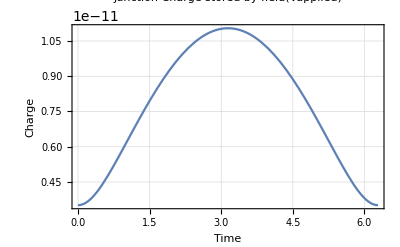

-Graphics-

1.05315×10^-10

-indexchangemodulator+referenceArmPhase

```mathematica
Height=220 10^-9;
lPi =2.048 10^-3; 
time=.
(*=============*)
Qstored=Height lPi pDope ( DepletionZoneT[ Vapplied] )q 
g0=Qstored/. Vapplied->0.001;
Print[ "0 volts Charged stored=",g0];
gR4 =Qstored/.  Vapplied->((-4));
 Print[ "-4 volts Charged stored=",gR4];
effBandCapacitance=  (g0-gR4)/(- 4);
Print["^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^"];
Print["The effective system capacitance for V=>(-4,0)is given by Ceff=",effBandCapacitance]
Print["^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^^"]
gAC=Qstored/.Vapplied->( -4(1-Cos[time]))

Plot[gAC,{time,0,2 Pi}, Frame-> True, PlotLabel-> "Junction Charge stored by field(Vapplied)",GridLines->Automatic, FrameLabel->{"Time", "Charge"}]
Plot[( 220 10^-9 2.048 10^-3 epsilonO epsilonR  DepletionZoneT[ Vapplied/Sqrt[2]]^-1),{time,0,2Pi}]
referenceArmIndex=Nsilicon= epsilonR epsilonO
signal= referenceArmPhase-indexchangemodulator
```

```mathematica
(*=============*)
(* Results from OptSim simulator on a E18 Custom Phase Shifter 2.048mm *)
BandwidthOptSim=34.2768 "GHz"(* GHz *)
 Print[ "Wd method effective capacitance 25 Ohm RF load= ",EngineeringForm[cWdR25L1]]
Print["Integrate gen functionVrms method 25 Ohm RF load= ", EngineeringForm[wcLibR25L1]]
Print[TableForm[{BandwidthOptSim,EngineeringForm[wcWdR25L1], EngineeringForm[wcLibR25L1]}]]
r2Bandwidth=TableForm[{{"2 ohm d.c load effective Bandwidth"},{"Wd QMethod",cWdR2L1},{"HalfPeriod QMethod", wcLibR2L1}}]
```

34.2768 GHz

Wd method effective capacitance 25 Ohm RF load= cWdR25L1

Integrate gen functionVrms method 25 Ohm RF load= 35.117×10^9

34.2768 GHz
wcWdR25L1
35.117×10^9

2 ohm d.c load effective Bandwidth | 
Wd QMethod | cWdR2L1
HalfPeriod QMethod | 4.38962×10^11

```mathematica
(*=============*)
L=1;
R=2;
Print["R=",R,"L=",L]
W0=Sqrt[effBandCapacitance]^-1;
Print["wo=",EngineeringForm[W0]]
Q=W0 L/R;
Print["Q=",EngineeringForm[Q]]
WC=1/(effBandCapacitance R);
cWdR2L1=WC
Print["Rc Cutoff 3dB=",EngineeringForm[WC]]
(*=============*)
(*****)
(*=============*)
L=1;
R=25;
Print["R=",R,"L=",L]
wcWdR25L1=WC;
Q=W0 L/R;
W0=Sqrt[effBandCapacitance]^-1;
Print["wo=",EngineeringForm[W0]]
Q=W0 L/R;
Print["Q=",EngineeringForm[Q]]
WC=1/(effBandCapacitance R);

Print["Homework \nCalculate the capcitance & effective index change vs impressed Voltage"]
```

R=2L=1

wo=924.205×10^3

Q=462.102×10^3

4.27077×10^11

Rc Cutoff 3dB=427.077×10^9

R=25L=1

wo=924.205×10^3

Q=36.9682×10^3

Homework 
Calculate the capcitance & effective index change vs impressed Voltage

```mathematica
Print["Rc Cutoff 3dB=",EngineeringForm[wcWdR25L1]];
(*=============*)
(* Results from OptSim simulator on a E18 Custom Phase Shifter 2.048mm *)
BandwidthOptSim=34.2768 "GHz"(* GHz *);
 Print[ "Wd method effective capacitance 25 Ohm RF load= ",EngineeringForm[cWdR25L1]];
Print["Integrate gen functionVrms method 25 Ohm RF load= ", EngineeringForm[wcLibR25L1]];
Print[TableForm[{BandwidthOptSim,EngineeringForm[wcWdR25L1], EngineeringForm[wcLibR25L1]}]];
r2Bandwidth=TableForm[{{"2 ohm d.c load effective Bandwidth"},{"Wd QMethod",cWdR2L1},{"HalfPeriod QMethod", wcLibR2L1}}];
```

Rc Cutoff 3dB=427.077×10^9

Wd method effective capacitance 25 Ohm RF load= cWdR25L1

Integrate gen functionVrms method 25 Ohm RF load= 35.117×10^9

34.2768 GHz
427.077×10^9
35.117×10^9